```mathematica
SetDirectory[NotebookDirectory[]];
Remove["Global`*"]//Quiet;
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"lib_v_3.nb"}],InsertResults->False];
```

# Teoria gier

## Notacja

Wypłata. W pierwszej kolejności jest prowadzna notacja oraz częściowo przypomniana notacja. Wypłata gracza i∈ℐ w profilu strategii s∈S jest dana wzorem

u_i(s)=∑_(a∈A) p(s,a)·u_i(a),

gdzie p(s,a) to prawdopodobieństwo wystąpienia profilu akcji a∈A jeżeli grany jest profil strategii s. Jak określony jest już profil akcji a to z definicji określona jest wypłata graczy a więc w szczególności gracza i-tego. Podobnie można oznaczyć p(s_-i,a_-i) jeżeli chcemy mieć prawdopodobieństwo, że zdarzy się profil akcji a_-i przy profilu strategii s_-i gdzie w obu profilach został pominięty gracz i∈ℐ.

Dodatkowe proste funkcje. Jeżeli dany jest profil strategii s, w którym dla gracza i∈ℐ zamienimy jego strategię s_i na akcję j-tą, oznaczaną przez a_ij∈A_i, to jego wypłata będzie oznaczana przez

x_ij(s)=u_i(a_ij,s_-i)=∑_(a_-i∈A_-i) p(s_-i,a_-i)·u_i(a_ij,a_-i).

Następnie definiujemy funkcję

z_ij(s)=x_ij(s)-u_i(s).

Jest to różnica, dla gracza i∈ℐ, pomiędzy graniem w profilu s, j-tej akcji zamiast strategii s_i. Warto zauważyć, że jeżeli profil strategii s jest równowagą Nasha, a akcja a_ij należy do nośnika tej równowagi Nasha, to zachodzi z_ij(s)=0. Jeżeli profil s jest równowagą Nasha a akcja a_ij nie należy do jej nośnika to zawsze musi zachodzić z_ij(s)≤0, gdzie 0 może zachodzić jeżeli dwie akcje dają te same wypłaty (ale np. nie wprzypadku strict Nasha equilibria, które są zawsze w akcjach). Jeżeli istnieje jakiś gracz i oraz jakaś jego akcja a_ij, dla której z_ij(s)>0 to profil s nie jest równowagą Nasha.

Ostatecznie definiujemy funkcję

g_ij(s)=max{z_ij(s),0}.

Jedyna różnica w stosunku do funkcji z_ij(s) jest taka, że ta funkcja nie może przyjmować wartości ujemnych.

## Charakteryzacja równowagi Nasha

Poprzednim razem wykorzystywaliśmy pewną charakteryzację równowagi Nasha ale tylko jeżeli chodzi o gry symetryczne. Dokładnie taka sama jest charakteryzacja równowagi Nasha w dowolnej grze (w postaci normalnej, skończonej). Niech

v(s)=∑_(i∈ℐ) ∑_(1≤j≤𝒶_i) (g_ij(s))^2,

gdzie 𝒶_i jest liczbą akcji gracza i∈ℐ. Powyższa funkcja jest różniczkowalna oraz v(s)≥0 dla dowolnego s.

Fakt. Profil strategii s jest równowagą Nasha wtedy i tylko wtedy jeżeli v(s)=0.

Uwaga. Podobnie jak w poprzednim wykładzie, można wykorzystać powyższy fakt do konstrukcji algorytmu szukającego równowagi Nasha, tym razem w dowolnych grach, który jest oparty na minimalizacji funkcji v na S.

Można jednak wykorzystać funkcję v do bardzo szybkiej weryfikacji czy dany profil s jest równowagą Nasha. To wykorzystamy w drugim algorytmie w tym wykładzie.

## Algorytmy

Algorytm 1. Jako pierwszy algorytm, rozważymy algorytm oparty o optymalizację. Jest to algorytm, który dla zadanej gry wybiera losowy profil s i traktuje go jako punkt początkowy procedury optymalizacji. Ewentualnie można zastosować tzw. globalne procedury optymalizacji.

W takiej procedurze jako dane wejściowe powinny zostać przekazane następujące argumenty: gra, procedura optymaliacji, punkt początkowy (opcjonalnie, jeżeli nie jest przekazany to może być wybrany losowo).

Algorytm 2. Drugi algorytm to tzw. algorytm szkolny. Na wstępnych wykładach z teorii gier pokazuje się, że skoro w równowadze Nasha, wszystkie akcje należące do nośnika muszą dawać takie same wypłaty to można na tej podstawie stworzyć odpowiednie układy równań, które po rozwiązaniu dają (potencjalnie) równowagi Nasha. Pomysł zatem jest taki aby algorytm dla wszystkich możliwych nośników tworzył odpowiedni układ równań liniowych i rozwiązywał go (z oczywistymi ograniczeniami). Po uzyskaniu takiej potencjalnej równowagi Nasha s można obliczyć wartość v(s) i zweryfikować czy uzyskane rozwiązanie rzeczywiście jest równowagą Nasha. Algorytm ten nie nadaje się do dużych gier ze względu na gigantyczną liczbę wszystkich nośników dla dużych gier ale dla małych gier jest do przejścia.

W takiej procedurze jako dane wejściowe powinny zostać przekazane następujące argumenty: gra.

## Implementacje

### Reprezentacja

Implementacja. W pierwszej kolejności trzeba zaproponować ogólną implementację obliczania funkcji v.

```mathematica
ClearAll[computeV]
computeV[game_,profile_]:=Module[{numOfPlayer,numOfActions,playerActions,uAtProfile,uAtActions,player,temp,v=0,k},
(* liczba graczy *)
numOfPlayer=Length[game];
(* liczba akcji dla każdego gracza *)
numOfActions=Dimensions[game["player 1"]];
(* wypłata w profilu *)
uAtProfile=getPayoff[game,profile];
(* obliczanie v *)
For[player=1,player≤numOfPlayer,player++,
temp=profile;
(* wypłat dla akcji dla danego gracza *)
playerActions=IdentityMatrix[numOfActions⟦player⟧];
uAtActions=getPayoff[game,#]⟦player⟧&/@Table[temp⟦player⟧=playerActions⟦k⟧; temp,{k,1,numOfActions⟦player⟧}];
(* przekształcania *)
v=v+Total[(Max[0,#]^2)&/@(uAtActions-uAtProfile⟦player⟧)]
];
v
]
```

Przykład. Zdefiniujemy trzy-osobową grę koordynacyjną.

```mathematica
g1=<|"player 1"->{{{1,0},{0,0}},{{0,0},{0,1}}},"player 2"->{{{1,0},{0,0}},{{0,0},{0,1}}},"player 3"->{{{1,0},{0,0}},{{0,0},{0,1}}}|>;
MatrixForm/@g1
```

<|player 1→((1
0) | (0
0)
(0
0) | (0
1)),player 2→((1
0) | (0
0)
(0
0) | (0
1)),player 3→((1
0) | (0
0)
(0
0) | (0
1))|>

Jest to prosta gra symmetryczna, gdzie gracze dostają wszyscy 1 jeżeli grają tę samą akcję (dowolną ale tę samą) oraz 0 w przeciwnym przypadku. Obliczmy jak będzie wyglądała funkcja v.

```mathematica
ClearAll[x,y,z]
```

```mathematica
v1=computeV[g1,{{x,1-x},{y,1-y},{z,1-z}}]//Simplify
```

Max[0,-(-1+x+y) (-1+z)]^2+Max[0,-(-1+x+y) z]^2+Max[0,-(-1+y) (-1+x+z)]^2+Max[0,-y (-1+x+z)]^2+Max[0,-(-1+x) (-1+y+z)]^2+Max[0,-x (-1+y+z)]^2

Korzystając z powyższej funkcji można łatwo obejrzeć gdzie potencjalnie znajdują się jej zero (a więc minima globalne).

```mathematica
ContourPlot3D[v1,{x,0,1},{y,0,1},{z,0,1},Contours->Table[1/k,{k,{10,20,30,40,50}}],Mesh->None,ContourStyle->Opacity[0.5]]
```

-Graphics3D-

Widzimy, że mamy tutaj trzy równowagi Nasha: wszyscy grają pierwszą akcję, wszyscy grają drugą akcję albo wszyscy grają strategię (1/2,1/2). Możemy się o tym łatwo przekonać sprawdzając wartości funkcji v bezpośrednio.

```mathematica
computeV[g1,{{1,0},{1,0},{1,0}}]
```

0

```mathematica
computeV[g1,{{0,1},{0,1},{0,1}}]
```

0

```mathematica
computeV[g1,{{1/2,1/2},{1/2,1/2},{1/2,1/2}}]
```

0

Możemy też testować różne pytania. Przykładowo, jeżeli trzeci gracz gra strategię (1/2,1/2) to jakie strategie muszą grać pozostali gracze aby dostać równowagę Nasha?

```mathematica
v1=computeV[g1,{{x,1-x},{y,1-y},{1/2,1/2}}]//Simplify
```

Max[0,1/2 (1-x-y)]^2+Max[0,-1/2 (-1+2 x) (-1+y)]^2+Max[0,1/2 (-1+x+y)]^2+Max[0,-1/2 (-1+x) (-1+2 y)]^2+Max[0,x/2-x y]^2+Max[0,y/2-x y]^2

```mathematica
Plot3D[
v1,
{x,0,1},{y,0,1},
Exclusions->None,
MeshFunctions->{#3&},
PlotPoints->30
]
```

-Graphics3D-

Jak widać mamy tutaj jedyny punkt zerowy (1/2,1/2). Ciekawe zatem, że mamy tutaj tylko trzy równowagi i wszystkie są symetryczne.

Przykład. Zdefiniujemy trzy osobową grę anty-koordynacyjną.

```mathematica
g2=<|"player 1"->{{{0,1},{1,1}},{{1,1},{1,0}}},"player 2"->{{{0,1},{1,1}},{{1,1},{1,0}}},"player 3"->{{{0,1},{1,1}},{{1,1},{1,0}}}|>;
MatrixForm/@g2
```

<|player 1→((0
1) | (1
1)
(1
1) | (1
0)),player 2→((0
1) | (1
1)
(1
1) | (1
0)),player 3→((0
1) | (1
1)
(1
1) | (1
0))|>

Jest to prosta gra symetryczna, w której wszyscy gracze otrzymują 1 jeżeli tylko nie wszyscy grają to samo. Jeżeli wszyscy grają tę samą akcję, wtedy wszyscy otrzymują 0. Podobnie jak powyżej, obliczymy funkcję v.

```mathematica
ClearAll[x,y,z]
```

```mathematica
v2=computeV[g2,{{x,1-x},{y,1-y},{z,1-z}}]//Simplify
```

Max[0,(-1+x+y) (-1+z)]^2+Max[0,(-1+x+y) z]^2+Max[0,(-1+y) (-1+x+z)]^2+Max[0,y (-1+x+z)]^2+Max[0,(-1+x) (-1+y+z)]^2+Max[0,x (-1+y+z)]^2

Korzystając z powyższej funkcji można łatwo obejrzeć gdzie potencjalnie znajdują się jej zero (a więc minima globalne).

```mathematica
fig1=ContourPlot3D[v2,{x,0,1},{y,0,1},{z,0,1},Contours->Table[1/k,{k,{3000}}],Mesh->None,ContourStyle->Opacity[0.5],MaxRecursion->2,PlotPoints->20]
```

-Graphics3D-

Nie jest bardzo jasne gdzie tutaj są zera funkcji v ale możemy podejrzewać, że zbiory zer, a więc również równowag Nasha, będą się układały wzdłuż krawędzi rzutu iloczynu sympleksów. Jeżeli jeden gracz gra pierwszą strategię a inny drugą strategię to pozostały jest obojętny pomiędzy nimi a więc może grać cokolwiek. To będzie tworzyło komponenty. Oprócz tego mamy jeszcze strategię mieszaną symetryczna opartą o strategię (1/2,1/2). Możemy sprawdzić jak zachowuje się ta funkcja w zależności od parametru z.

```mathematica
Manipulate[
Plot3D[
v2/.z->ztemp,
{x,0,1},{y,0,1},
Exclusions->None,
MeshFunctions->{#3&},
PlotPoints->50,
ClippingStyle->Opacity[0.5],
PlotRange->{0,htemp}
],
{{ztemp,0,"z"},0,1},
{{htemp,1,"wysokość"},1/1000,1}
]
```

Powyższy przykład pokazuje, że wyzwania stojące przed procedurami optymalizacji są tutaj bardzo duże bo mamy tutaj całe komponenty zer oraz jedno zero izolowane. Poza tym, funkcja w wielu miejscach będzie miała gradienty bardzo bliskie zera a więc zbieżności będą bardzo wolne.

### Dodatkowe funkcje techniczne

Implementacja. W następnej kolejności chcemy zaimplementować funkcję, która znajduje równowagi Nasha na podstawie optymalizacji. Zanim to jednak zrobimy potrzemujemy kilku technicznych funkcji.

```mathematica
ClearAll[simplex]
simplex[n_,var_]:=Module[{vars,k},
vars=Table[var[k],{k,1,n-1}];
ImplicitRegion[Append[(#≥0)&/@vars,Total[vars]≤1],Evaluate[vars]]
]
```

```mathematica
ClearAll[region]
region[dims_,var_]:=Module[{ret,vars},
vars=Table[var[k],{k,1,Length[dims]}];
RegionProduct@@MapThread[simplex,{dims,vars}]
]
```

Przykład. Powyższe funkcje są konieczne do tworzenie poprawnych ograniczeń, które są dalej wykorzystywane przy optymalizacji. Zdefiniujemy wygodne formatowania dla zmiennych.

```mathematica
Clear[x]
Format[x[s_]]:=Style[Subscript[x, Style[s,Bold]],Blue]
Format[x[s_][r_]]:=Style[Subscript[x, Style[s,Bold],r],Blue]
```

Pierwsza z powyższych funkcji zwraca sympleks (dokładniej to rzut prostopadły) zadany w odpowiednich zmiennych. Poniżej jest kilka takich prostych przykładów.

ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}]

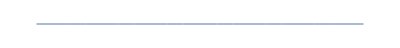

```mathematica
simplex[2,x[1]]
Region[%]
```

ImplicitRegion[x_(1,1)≥0&&x_(1,2)≥0&&x_(1,1)+x_(1,2)≤1,{x_(1,1),x_(1,2)}]

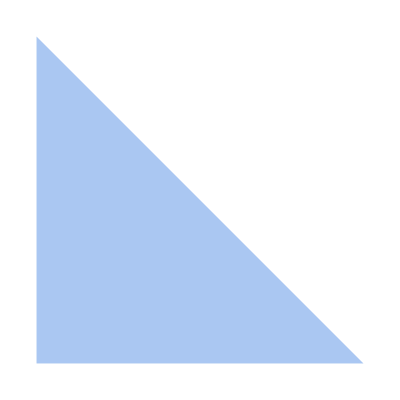

```mathematica
simplex[3,x[1]]
Region[%]
```

```mathematica
simplex[4,x[1]]
Region[%]
```

ImplicitRegion[x_(1,1)≥0&&x_(1,2)≥0&&x_(1,3)≥0&&x_(1,1)+x_(1,2)+x_(1,3)≤1,{x_(1,1),x_(1,2),x_(1,3)}]

-Graphics3D-

Druga z powyższych funkcji zwraca odpowiedni iloczyn kartezjański sympleksów, na podstawie listy liczby akcji dla kolejnych graczy. Poniżej jest kilka typowych przykładów.

RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}]]

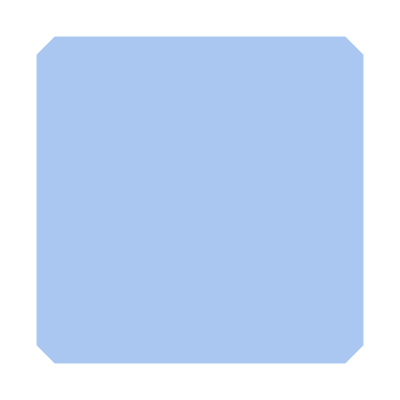

```mathematica
region[{2,2},x]
Region[%]
```

```mathematica
region[{2,2,2},x]
Region[%]
```

RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]]

-Graphics3D-

```mathematica
region[{2,3},x]
Region[%]
```

RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,2)≥0&&x_(2,1)+x_(2,2)≤1,{x_(2,1),x_(2,2)}]]

-Graphics3D-

```mathematica
region[{3,2},x]
Region[%]
```

RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,2)≥0&&x_(1,1)+x_(1,2)≤1,{x_(1,1),x_(1,2)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}]]

-Graphics3D-

### Algorytm 1

Implementacja. Mając gotowe funkcje do tworzenie ograniczeń możemy zaimplementować główną funkcję do znajdowania równowag Nasha.

```mathematica
ClearAll[findNashEquilibriaThroughMinimization,optMethod,zeroThreshold]
Options[findNashEquilibriaThroughMinimization]={optMethod->Automatic,zeroThreshold->10^(-5)};
findNashEquilibriaThroughMinimization[game_,var_,OptionsPattern[]]:=Module[{reg,vars,varsFlat,profile,target,sol},
reg=region[Dimensions[game["player 1"]],var];
vars=Last/@List@@reg;
varsFlat=Flatten[vars];
profile=(Append[#,1-Total[#]])&/@vars;
target=computeV[game,profile];
(* optymalizacja *)
(* metoda automatyczna *)
If[MemberQ[{Symbol},Head[OptionValue[optMethod]]],
sol=NMinimize[{target,varsFlat∈reg},varsFlat,Method->{"NelderMead","InitialPoints"->RandomPoint[reg,1]}]
];
(* metoda podana *)
If[!MemberQ[{Symbol},Head[OptionValue[optMethod]]],
sol=NMinimize[{target,varsFlat∈reg},varsFlat,Method->OptionValue[optMethod]]
];
(* weryfikacja czy znalezione minimum jest zerem *)
If[First[sol]>OptionValue[zeroThreshold],sol=Nothing];
(* zwracanie *)
<|
"region"->reg,
"vars optimization"->varsFlat,
"profile"->profile,
"target"->target,
"solution"->sol
|>
]
```

Przykład. Powyższa funkcja może być różnie wywoływana. Wywołanie bez podania metody wykorzystana standardowe podejście.

```mathematica
ne1=findNashEquilibriaThroughMinimization[g1,x]
```

<|region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]],vars optimization→{x_(1,1),x_(2,1),x_(3,1)},profile→{{x_(1,1),1-x_(1,1)},{x_(2,1),1-x_(2,1)},{x_(3,1),1-x_(3,1)}},target→Max[0,(1-x_(1,1)) (1-x_(2,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,x_(1,1) x_(2,1)-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,(1-x_(1,1)) (1-x_(3,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,(1-x_(2,1)) (1-x_(3,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))+x_(1,1) x_(3,1)-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))+x_(2,1) x_(3,1)-x_(1,1) x_(2,1) x_(3,1)]^2,solution→{5.21201×10^-18,{x_(1,1)→0.5,x_(2,1)→0.5,x_(3,1)→0.5}}|>

```mathematica
MatrixForm/@ne1["profile"]/.ne1["solution"]⟦2⟧
```

{(0.5
0.5),(0.5
0.5),(0.5
0.5)}

Można jednak wykorzystać bardzo dokładne strojenie metod. Poniżej wywołanie z losowym przeszukiwaniem.

```mathematica
ne1a=findNashEquilibriaThroughMinimization[g1,x,optMethod->"RandomSearch"]
```

<|region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]],vars optimization→{x_(1,1),x_(2,1),x_(3,1)},profile→{{x_(1,1),1-x_(1,1)},{x_(2,1),1-x_(2,1)},{x_(3,1),1-x_(3,1)}},target→Max[0,(1-x_(1,1)) (1-x_(2,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,x_(1,1) x_(2,1)-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,(1-x_(1,1)) (1-x_(3,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,(1-x_(2,1)) (1-x_(3,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))+x_(1,1) x_(3,1)-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))+x_(2,1) x_(3,1)-x_(1,1) x_(2,1) x_(3,1)]^2,solution→{3.16624×10^-25,{x_(1,1)→0.5,x_(2,1)→0.5,x_(3,1)→0.5}}|>

```mathematica
MatrixForm/@ne1a["profile"]/.ne1a["solution"]⟦2⟧
```

{(0.5
0.5),(0.5
0.5),(0.5
0.5)}

Możemy jednak nieco bardziej wysterować metodę optymalizacji.

```mathematica
ne1b=findNashEquilibriaThroughMinimization[g1,x,
optMethod->{"RandomSearch",
"SearchPoints"->1,
"InitialPoints"->{{.9,.9,.9}},
"Method"->"InteriorPoint"}]
```

<|region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]],vars optimization→{x_(1,1),x_(2,1),x_(3,1)},profile→{{x_(1,1),1-x_(1,1)},{x_(2,1),1-x_(2,1)},{x_(3,1),1-x_(3,1)}},target→Max[0,(1-x_(1,1)) (1-x_(2,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,x_(1,1) x_(2,1)-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,(1-x_(1,1)) (1-x_(3,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,(1-x_(2,1)) (1-x_(3,1))-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))+x_(1,1) x_(3,1)-x_(1,1) x_(2,1) x_(3,1)]^2+Max[0,-(1-x_(1,1)) (1-x_(2,1)) (1-x_(3,1))+x_(2,1) x_(3,1)-x_(1,1) x_(2,1) x_(3,1)]^2,solution→{1.66315×10^-16,{x_(1,1)→1.,x_(2,1)→1.,x_(3,1)→1.}}|>

```mathematica
MatrixForm/@ne1b["profile"]/.ne1b["solution"]⟦2⟧
```

{(1.
7.44569×10^-9),(1.
7.44569×10^-9),(1.
7.44569×10^-9)}

Manipulując zarówno algorytmami jak i ich parametrami uzyskaliśmy wszystkie równowagi Nasha. Oczywiście możemy również wielokrotnie powtarzać procedurę z losowymi parametrami co również może nam dać wszystkie równowagi Nasha (w prostych grach).

```mathematica
ParallelTable[
temp=findNashEquilibriaThroughMinimization[g1,x];Round[temp["profile"]/.temp["solution"]⟦2⟧,0.01],
{500}]//DeleteDuplicates//Grid
```

{0.5,0.5} | {0.5,0.5} | {0.5,0.5}
{1.,0.} | {1.,0.} | {1.,0.}
{0.,1.} | {0.,1.} | {0.,1.}

Przykład. Pierwsza z rozpatrywanych gier jest naprawdę raczej prosta. Druga z nich, również bardzo prosta, postawi przed powyższym algorytmem znacznie większe problemy.

```mathematica
ne2=findNashEquilibriaThroughMinimization[g2,x];
ne2["solution"]
```

{2.45694×10^-19,{x_(1,1)→0.998007,x_(2,1)→4.95129×10^-10,x_(3,1)→1.}}

Zobaczmy gdzie układają się znalezione równowagi Nasha.

```mathematica
ps=ParallelTable[
temp=findNashEquilibriaThroughMinimization[g2,x];
temp["vars optimization"]/.temp["solution"]⟦2⟧,
{500}]//DeleteDuplicates;
```

```mathematica
Show[fig1,Graphics3D[{
Blue,PointSize[Medium],Point[ps]
}]]
```

-Graphics3D-

Możemy wykorzytać inną metodę optymalizacji i bardzo dokładnie sterować początkiem startu optymalizacji i otrzymać w praktyce dowolną równowagę Nasha ale musimy wiedzieć gdzie należy wystartować algorytm.

```mathematica
ne2a=findNashEquilibriaThroughMinimization[g2,x,
optMethod->{"SimulatedAnnealing",
"SearchPoints"->1,
"InitialPoints"->{{.99,0.01,.25}},
"PerturbationScale"->1/10
}];
ne2a["profile"]/.ne2a["solution"]⟦2⟧
```

{{1.,1.2177×10^-8},{1.05895×10^-8,1.},{0.249835,0.750165}}

Takie podejście może być praktyczne przy relatywie skomplikowanych grach, gdzie z przyczyn modelowych wiemy gdzie mniej więcej musi znajdować się równowaga.

Przykład.  Mając powyższą technologię możemy popatrzeć sobie na jakieś losowe gry.

```mathematica
g3=generateRandomGame[BinomialDistribution[10,1/2],{2,2,2}];
MatrixForm/@g3
```

<|player 1→((5
3) | (3
8)
(5
5) | (5
5)),player 2→((4
5) | (4
7)
(4
7) | (4
5)),player 3→((3
4) | (4
8)
(4
3) | (6
5))|>

```mathematica
v3=computeV[g3,{{x,1-x},{y,1-y},{z,1-z}}]//Simplify
```

Max[0,-2 (-1+2 x) (-1+y) (-1+z)]^2+Max[0,-(1-5 x+3 x y) (-1+z)]^2+Max[0,(-1+5 x-3 x y) z]^2+Max[0,2 y (-1+2 x+z-2 x z)]^2+Max[0,x (-3+5 y+5 z-7 y z)]^2+Max[0,-(-1+x) (3-5 y-5 z+7 y z)]^2

```mathematica
fig2=ContourPlot3D[v3,{x,0,1},{y,0,1},{z,0,1},Contours->Table[1/k,{k,{1,2,10,3000}}],Mesh->None,ContourStyle->Opacity[0.5],MaxRecursion->2,PlotPoints->20]
```

-Graphics3D-

```mathematica
ps=ParallelTable[
findNashEquilibriaThroughMinimization[g3,x]["solution"],
{500}];
ps=(Last/@#)&/@(Last/@ps);
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Show[fig2,Graphics3D[{
Blue,PointSize[Medium],Point[ps]
}]]
```

-Graphics3D-

### Algorytm 2

Implementacja. Proste funkcje pomocnicze.

```mathematica
ClearAll[profileFull]
profileFull[dim_,var_]:=Module[{ret,p,j,temp},
ret=Table[
Table[var[p][j],
{j,1,dim⟦p⟧}],
{p,1,Length[dim]}];
ret
]
```

```mathematica
ClearAll[profileP]
profileP[dim_,player_,var_]:=Module[{ret,p,j,temp},
ret=Table[
Table[var[p][j],
{j,1,dim⟦p⟧}],
{p,1,Length[dim]}];
Table[
temp=ret;
temp⟦player⟧=IdentityMatrix[dim⟦player⟧]⟦j⟧;
temp,
{j,1,dim⟦player⟧}]
]
```

Przykład. Z teoretycznego punktu widzenia algorytm oparty o rozwiązywanie układów równań jest a następnie weryfikację czy otrzymane rozwiązanie jest poprawne, wydaje się relatywnie prosty ale niestety tak nie jest. Zaczniemy od prostego przykładu. Definiujmey prostą grę.

```mathematica
g1=<|
"player 1"->{{1,0},{0,1}},
"player 2"->{{1,0},{0,1}}
|>;
MatrixForm/@g1
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

Wyznaczamy przykładowy układ równań.

```mathematica
sys1={
Equal@@(First/@(getPayoff[g1,#]&/@profileP[Dimensions[g1["player 1"]],1,x])),
Equal@@(Last/@(getPayoff[g1,#]&/@profileP[Dimensions[g1["player 1"]],2,x]))
}
```

{x_(2,1)==x_(2,2),x_(1,1)==x_(1,2)}

Dodajemy standardowe warunki dotyczące rozkładów prawdopodobieństwa.

```mathematica
prof1=profileFull[Dimensions[g1["player 1"]],x]
```

{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)}}

```mathematica
sys1cond1=(Total[#]==1)&/@prof1
sys1cond2=(#≥0)&/@Flatten[prof1]
```

{x_(1,1)+x_(1,2)==1,x_(2,1)+x_(2,2)==1}

{x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0,x_(2,2)≥0}

Jeżeli wykorzystamy wszystkie konieczne warunki to otrzymamy następujący układ warunków.

```mathematica
prob1a=Join[sys1,sys1cond1]
```

{x_(2,1)==x_(2,2),x_(1,1)==x_(1,2),x_(1,1)+x_(1,2)==1,x_(2,1)+x_(2,2)==1}

Następnie możemy wykorzystać taki układ do znalezienia rozwiązania.

```mathematica
sol1=Solve[prob1a,Flatten[prof1]]
```

{{x_(1,1)→1/2,x_(1,2)→1/2,x_(2,1)→1/2,x_(2,2)→1/2}}

I ostatecznie zweryfikować czy otrzymane rozwiązanie jest równowagą Nasha.

```mathematica
computeV[g1,prof1/.sol1⟦1⟧]
```

0

Wydaje się więc, że taka procedura działa i jest relatywnie prosta do implementacji (modulo funkcja Solve[]). Przekonamy się o tym w następnym przykładzie.

Przykład. Trochę bardziej skomplikowany przykład.

```mathematica
g2=<|
"player 1"->{{1,1},{0,1}},
"player 2"->{{1,1},{0,1}}
|>;
MatrixForm/@g2
```

<|player 1→(1 | 1
0 | 1),player 2→(1 | 1
0 | 1)|>

Wyznaczamy przykładowy układ równań.

```mathematica
sys2={
Equal@@(First/@(getPayoff[g2,#]&/@profileP[Dimensions[g2["player 1"]],1,x])),
Equal@@(Last/@(getPayoff[g2,#]&/@profileP[Dimensions[g2["player 1"]],2,x]))
}
```

{x_(2,1)+x_(2,2)==x_(2,2),x_(1,1)==x_(1,1)+x_(1,2)}

Dodajemy standardowe warunki dotyczące rozkładów prawdopodobieństwa.

```mathematica
prof2=profileFull[Dimensions[g2["player 1"]],x]
```

{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)}}

```mathematica
sys2cond1=(Total[#]==1)&/@prof2
sys2cond2=(#≥0)&/@Flatten[prof2]
```

{x_(1,1)+x_(1,2)==1,x_(2,1)+x_(2,2)==1}

{x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0,x_(2,2)≥0}

Jeżeli wykorzystamy wszystkie konieczne warunki to otrzymamy następujący układ warunków.

```mathematica
prob2a=Join[sys2,sys2cond1,sys2cond2]
```

{x_(2,1)+x_(2,2)==x_(2,2),x_(1,1)==x_(1,1)+x_(1,2),x_(1,1)+x_(1,2)==1,x_(2,1)+x_(2,2)==1,x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0,x_(2,2)≥0}

Następnie możemy wykorzystać taki układ do znalezienia rozwiązania.

```mathematica
sol2=Solve[prob2a,Flatten[prof2]]
```

{{x_(1,1)→1,x_(1,2)→0,x_(2,1)→0,x_(2,2)→1}}

I ostatecznie zweryfikować czy otrzymane rozwiązanie jest równowagą Nasha.

```mathematica
computeV[g2,prof2/.sol2⟦1⟧]
```

0

Problem z takim podejściej jak widać jest taki, że to co się otrzymuje to niestety nie jest pełen zbiór równowag Nasha.

Przykład. Trochę bardziej skomplikowany przykład.

```mathematica
g2=<|
"player 1"->{{1,1},{0,1}},
"player 2"->{{0,1},{0,1}}
|>;
MatrixForm/@g2
```

<|player 1→(1 | 1
0 | 1),player 2→(0 | 1
0 | 1)|>

Wyznaczamy przykładowy układ równań.

```mathematica
sys2={
Equal@@(First/@(getPayoff[g2,#]&/@profileP[Dimensions[g2["player 1"]],1,x])),
Equal@@(Last/@(getPayoff[g2,#]&/@profileP[Dimensions[g2["player 1"]],2,x]))
}
```

{x_(2,1)+x_(2,2)==x_(2,2),0==x_(1,1)+x_(1,2)}

Dodajemy standardowe warunki dotyczące rozkładów prawdopodobieństwa.

```mathematica
prof2=profileFull[Dimensions[g2["player 1"]],x]
```

{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)}}

```mathematica
sys2cond1=(Total[#]==1)&/@prof2
sys2cond2=(#≥0)&/@Flatten[prof2]
```

{x_(1,1)+x_(1,2)==1,x_(2,1)+x_(2,2)==1}

{x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0,x_(2,2)≥0}

Jeżeli wykorzystamy wszystkie konieczne warunki to otrzymamy następujący układ warunków.

```mathematica
prob2a=Join[sys2,sys2cond1,sys2cond2]
```

{x_(2,1)+x_(2,2)==x_(2,2),0==x_(1,1)+x_(1,2),x_(1,1)+x_(1,2)==1,x_(2,1)+x_(2,2)==1,x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0,x_(2,2)≥0}

Następnie możemy wykorzystać taki układ do znalezienia rozwiązania.

```mathematica
sol2=Solve[prob2a,Flatten[prof2]]
```

{}

Jak widać, tutaj nie znajdujemy żadnych rozwiązań z pełnym nośnikiem (ciekawe, że poprzednio znaleźliśmy, a więc nie jest to ogólna reguła). Oczywiście możemy wybrać inne nośniki (a więc algorytm ogólnie musi generować wszystkie możliwe nośniki a więc już ma złożoność na poziomie 2^𝒶, gdzie 𝒶 to generyczna liczba akcji.  Dobierzmy inny nośnik.

```mathematica
g2=<|
"player 1"->{{1},{1}},
"player 2"->{{1},{1}}
|>;
MatrixForm/@g2
```

<|player 1→(1
1),player 2→(1
1)|>

Wyznaczamy przykładowy układ równań.

```mathematica
sys2={
Equal@@(First/@(getPayoff[g2,#]&/@profileP[Dimensions[g2["player 1"]],1,x])),
Equal@@(Last/@(getPayoff[g2,#]&/@profileP[Dimensions[g2["player 1"]],2,x]))
}
```

{True,True}

Dodajemy standardowe warunki dotyczące rozkładów prawdopodobieństwa.

```mathematica
prof2=profileFull[Dimensions[g2["player 1"]],x]
```

{{x_(1,1),x_(1,2)},{x_(2,1)}}

```mathematica
sys2cond1=(Total[#]==1)&/@prof2
sys2cond2=(#≥0)&/@Flatten[prof2]
```

{x_(1,1)+x_(1,2)==1,x_(2,1)==1}

{x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0}

Jeżeli wykorzystamy wszystkie konieczne warunki to otrzymamy następujący układ warunków.

```mathematica
prob2a=Join[sys2,sys2cond1,sys2cond2]
```

{True,True,x_(1,1)+x_(1,2)==1,x_(2,1)==1,x_(1,1)≥0,x_(1,2)≥0,x_(2,1)≥0}

Następnie możemy wykorzystać taki układ do znalezienia rozwiązania.

```mathematica
sol2=Solve[prob2a,Flatten[prof2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x_(1,2)→ConditionalExpression[1-x_(1,1), 0≤x_(1,1)≤1],x_(2,1)→1}}

I tutaj pojawia się drugi problem, gdzie dostajemy pewien zbiór jako wyrażenie warunkowe. Na każdy elementem tego zbioru należy nałożyć warunek z funkcji v.

```mathematica
computeV[g2,prof2/.sol2⟦1⟧]
Simplify[%,Assumptions->And@@Join[sys2cond1,sys2cond2]]
```

ConditionalExpression[0, 0≤x_(1,1)≤1]

0

Faktycznie dostajemy 0 dla każdego punktu spełniającego warunki. Algorytm ten jednak wymaga delikatnego przetwarzania wzorów i wyrażeń warunkowych co w WL jest do zrobienia ale w Julia raczej nie.